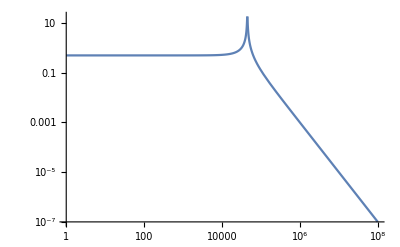

```mathematica
R1 = 0.1;
R3 = 0.1;
R2 = 1000;
L1 = 1*10^-3;
L2 = 1 * 10^-3;
C1 = 1 * 10^-6;

(* Překreslíme si odporový dělič *)
(* R1 a L1 se spojí do z1, R2, R3, L2 a C se paralelně spojí do z2 a ty se pak spojí do Z = z1 + z2 *)

(* Potřebujeme přenos A = Uout/U *)
(* Tento poměr můžeme získat pomocí z2/(z1 + z2) *)

z1 = R1 + ω*ⅉ*L1;
z2 = 1/(1/R2+1/(R3 + ⅉ*ω*L2)+ⅉ*ω*C1);

A = z2/(z1 + z2);
LogLogPlot[Abs[A], {ω, 1, 10^8}]
```